```mathematica
Exit[];
```

# Exploration: Polynomials

## Quadratic Polynomial

Our task is to find the coefficients of  an n^th order polynomial from n+1 points. Consider the following vector:

```mathematica
p[t_]:=a+b t+c t^2
```

We can find out values from three points: p(0), p(1), and p(2), form a linear system,

```mathematica
p[0]
```

a

```mathematica
p[1]
```

a+b+c

```mathematica
p[2]
```

a+2 b+4 c

We can now form a linear system with the form p[n]=AC, where p[n] are values from different points, A is the matrix of the linear system, and c is the coefficients vector.

```mathematica
A={{1,0,0},{1,1,1},{1,2,4}}
```

```mathematica
{{1,0,0},{1,1,1},{1,2,4}}
```

```mathematica
Inverse[A]
```

{{1,0,0},{-3/2,2,-1/2},{1/2,-1,1/2}}

```mathematica
pc={p0,p1,p2}
```

{p0,p1,p2}

```mathematica
Inverse[A].pc
```

{p0,-(3 p0)/2+2 p1-p2/2,p0/2-p1+p2/2}

Hence, we can see that p[t]=p[0]+(-(3 p[0])/2+2 p[1]-p[2]/2)t+(p[0]/2-p[1]+p[2]/2)t^2

```mathematica
Exit[];
```

## Cubic Polynomial

We can redo the entire process for a cubic polynomial.

```mathematica
p[t_]:=a+b t+c t^2+d t^3
```

```mathematica
p[0]
```

a

```mathematica
p[1]
```

a+b+c+d

```mathematica
p[2]
```

a+2 b+4 c+8 d

```mathematica
p[3]
```

a+3 b+9 c+27 d

Giving us the matrix of the linear system A

```mathematica
A={{1,0,0,0},{1,1,1,1},{1,2,4,8},{1,3,9,27}}
```

{{1,0,0,0},{1,1,1,1},{1,2,4,8},{1,3,9,27}}

```mathematica
pc = {p0, p1, p2,p3}
```

```mathematica
{p0,p1,p2,p3}
```

```mathematica
Inverse[A]
```

{{1,0,0,0},{-11/6,3,-3/2,1/3},{1,-5/2,2,-1/2},{-1/6,1/2,-1/2,1/6}}

```mathematica
Inverse[A] . pc
```

{p0,-(11 p0)/6+3 p1-(3 p2)/2+p3/3,p0-(5 p1)/2+2 p2-p3/2,-p0/6+p1/2-p2/2+p3/6}

```mathematica
Exit[];
```

## Quartic Polynomial

We can redo the entire process for a quartic polynomial.

```mathematica
p[t_]:=a+b t+c t^2+d t^3 + e t^4
```

```mathematica
p[0]
p[1]
p[2]
p[3]
p[4]
```

a

a+b+c+d+e

a+2 b+4 c+8 d+16 e

a+3 b+9 c+27 d+81 e

a+4 b+16 c+64 d+256 e

```mathematica
A = {{1, 0, 0, 0,0}, {1, 1, 1, 1,1}, {1, 2, 4, 8,16}, {1, 3, 9, 27,81},{1,4,16,64,256}}
```

{{1,0,0,0,0},{1,1,1,1,1},{1,2,4,8,16},{1,3,9,27,81},{1,4,16,64,256}}

```mathematica
pc = {p0, p1, p2, p3,p4}
```

{p0,p1,p2,p3,p4}

```mathematica
Inverse[A]
```

{{1,0,0,0,0},{-25/12,4,-3,4/3,-1/4},{35/24,-13/3,19/4,-7/3,11/24},{-5/12,3/2,-2,7/6,-1/4},{1/24,-1/6,1/4,-1/6,1/24}}

```mathematica
Inverse[A].pc
```

{p0,-(25 p0)/12+4 p1-3 p2+(4 p3)/3-p4/4,(35 p0)/24-(13 p1)/3+(19 p2)/4-(7 p3)/3+(11 p4)/24,-(5 p0)/12+(3 p1)/2-2 p2+(7 p3)/6-p4/4,p0/24-p1/6+p2/4-p3/6+p4/24}

```mathematica
Exit[];
```

## Arbitrary Function

```mathematica
p[t_]:=a (Cos[t])^3+b (Cos[t/2])^2+c
```

```mathematica
p[0]
p[1]
p[2]
```

a+b+c

c+b Cos[1/2]^2+a Cos[1]^3

c+b Cos[1]^2+a Cos[2]^3

```mathematica
A={{1,1,1},{Cos[1]^3,Cos[1/2]^2,1},{Cos[2]^3,Cos[1]^2,1}}
```

{{1,1,1},{Cos[1]^3,Cos[1/2]^2,1},{Cos[2]^3,Cos[1]^2,1}}

```mathematica
pc = {p0, p1, p2}
```

{p0,p1,p2}

```mathematica
Inverse[A].pc
```

{(p2 (1-Cos[1/2]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (Cos[1/2]^2-Cos[1]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (-1+Cos[1]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3),(p2 (-1+Cos[1]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (1-Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (-Cos[1]^3+Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3),(p2 (Cos[1/2]^2-Cos[1]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (-Cos[1]^2+Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (Cos[1]^5-Cos[1/2]^2 Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)}

Observe that although the expression is complicated, it is fully determined by the three points. How about if we try 0, pi, and 2pi as points?

```mathematica
p[0]
p[Pi]
p[2 Pi]
```

a+b+c

-a+c

a+b+c

Observe the linear dependence.

```mathematica
A={{1,1,1},{-1,0,1},{1,1,1}}
```

{{1,1,1},{-1,0,1},{1,1,1}}

```mathematica
Inverse[A].pc
```

Inverse::sing: Matrix {{1,1,1},{-1,0,1},{1,1,1}} is singular.

Inverse[{{1,1,1},{-1,0,1},{1,1,1}}].{p0,p1,p2}

It resulted into a singular matrix.

```mathematica
Exit[];
```

## Vector Space Test

```mathematica
p[t_]:=(Cos[t])^3
p[0]
p[1]
p[2]
```

1

Cos[1]^3

Cos[2]^3

```mathematica
cpc={{(p2 (1-Cos[1/2]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (Cos[1/2]^2-Cos[1]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (-1+Cos[1]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3),(p2 (-1+Cos[1]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (1-Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (-Cos[1]^3+Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3),(p2 (Cos[1/2]^2-Cos[1]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (-Cos[1]^2+Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (Cos[1]^5-Cos[1/2]^2 Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)}/.p0->1/.p1->Cos[1]^3/.p2->Cos[2]^3}//Simplify
```

{{1,0,0}}

```mathematica
q[t_]:=1(Cos[t])^3+0 (Cos[t/2])^2+0
```

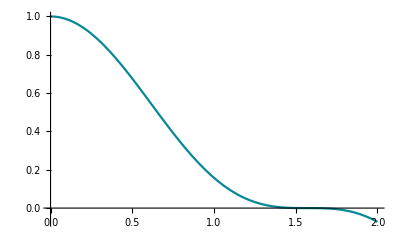

```mathematica
m=Plot[p[t],{t,0,2}]
```

```mathematica
n=Plot[q[t], {t, 0, 2}]
```

-Graphics-

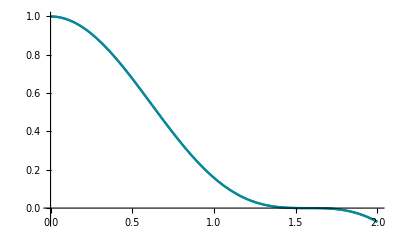

```mathematica
Show[m,n]
```

Both graphs are the same. Clearly, it is within the vector space.

```mathematica
Exit[];
```

```mathematica
p[t_]:=(Cos[3t])+(Sin[2t])
p[0]
p[1]
p[2]
```

1

Cos[3]+Sin[2]

Cos[6]+Sin[4]

```mathematica
cpc={{(p2 (1-Cos[1/2]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (Cos[1/2]^2-Cos[1]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (-1+Cos[1]^2))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3),(p2 (-1+Cos[1]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (1-Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (-Cos[1]^3+Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3),(p2 (Cos[1/2]^2-Cos[1]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p1 (-Cos[1]^2+Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)+(p0 (Cos[1]^5-Cos[1/2]^2 Cos[2]^3))/(Cos[1/2]^2-Cos[1]^2-Cos[1]^3+Cos[1]^5+Cos[2]^3-Cos[1/2]^2 Cos[2]^3)}/.p0->1/.p1->Cos[3]+Sin[2]/.p2->Cos[6]+Sin[4]}//Simplify
```

{{(Csc[1/2]^3 Sec[1/2] (Cos[1/2]-Sin[1/2]) (-Cos[3/2]-Cos[5/2]+Cos[7/2]+2 Sin[1/2]+3 Sin[3/2]-Sin[5/2]-Sin[7/2]))/(2 (1+2 Cos[1])^2),(Csc[1/2]^3 Sec[1/2] (5+6 Cos[1]-2 Cos[2]+Cos[3]+Cos[4]+Cos[5]-6 Sin[1]-3 Sin[2]+3 Sin[4]))/(4 (1+2 Cos[1])^2),-(Csc[1/2]^3 Sec[1/2] (6+8 Cos[1]+2 Cos[3]+2 Cos[4]+2 Cos[5]-6 Sin[1]-3 Sin[2]+3 Sin[4]))/(8 (1+2 Cos[1])^2)}}

```mathematica
q[t_]:=((Csc[1/2]^3 Sec[1/2] (Cos[1/2]-Sin[1/2]) (-Cos[3/2]-Cos[5/2]+Cos[7/2]+2 Sin[1/2]+3 Sin[3/2]-Sin[5/2]-Sin[7/2]))/(2 (1+2 Cos[1])^2)(Cos[t])^3)+((Csc[1/2]^3 Sec[1/2] (5+6 Cos[1]-2 Cos[2]+Cos[3]+Cos[4]+Cos[5]-6 Sin[1]-3 Sin[2]+3 Sin[4]))/(4 (1+2 Cos[1])^2)(Cos[t/2])^2)+(-(Csc[1/2]^3 Sec[1/2] (6+8 Cos[1]+2 Cos[3]+2 Cos[4]+2 Cos[5]-6 Sin[1]-3 Sin[2]+3 Sin[4]))/(8 (1+2 Cos[1])^2))
```

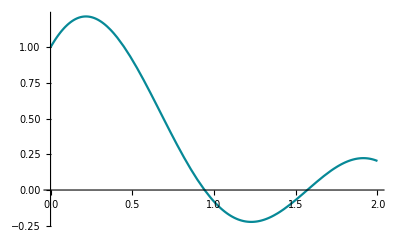

```mathematica
m=Plot[p[t], {t, 0, 2}]
```

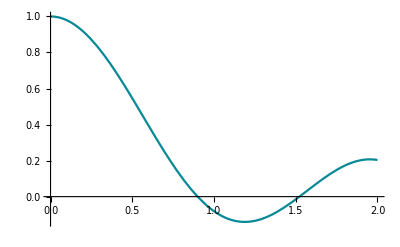

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot::pllim: Range specification Plot[q[t]] is not of the form {x, xmin, xmax}.

Show::gtype: Plot is not a type of graphics.

```mathematica
n=Plot[q[t], {t, 0, 2}]
```

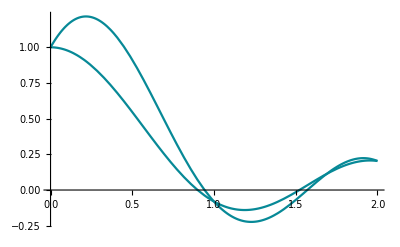

```mathematica
Show[m,n]
```

Does this mean that the said basis is not a basis? or is it just that the vector is outside the said vector space? They are not the same graphs.